Key data length: 60006

First 100 numbers of the key data: {6.61744×10^-24,0.,7.11204,0.364441,-4.78589,10.9432,0.0000333834,0.0000146937,7.11199,0.364445,-4.78588,10.9432,0.000133368,0.0000587013,7.11186,0.364454,-4.78585,10.9432,0.000300015,0.000132048,7.11163,0.36447,-4.78579,10.9431,0.000533332,0.000234733,7.11132,0.364492,-4.78571,10.943,0.000833329,0.000366757,7.11092,0.364521,-4.78561,10.9428,0.00120002,0.000528122,7.11043,0.364556,-4.78548,10.9426,0.00163343,0.000718827,7.10985,0.364597,-4.78534,10.9424,0.00213357,0.000938874,7.10918,0.364645,-4.78516,10.9421,0.00270047,0.00118826,7.10842,0.364699,-4.78497,10.9418,0.00333415,0.001467,7.10757,0.36476,-4.78476,10.9415,0.00403465,0.00177507,7.10663,0.364827,-4.78452,10.9411,0.004802,0.0021125,7.1056,0.3649,-4.78426,10.9407,0.00563624,0.00247927,7.10448,0.364979,-4.78397,10.9402,0.0065374,0.00287539,7.10327,0.365065,-4.78366,10.9397,0.00750554,0.00330086,7.10197,0.365158,-4.78333,10.9392,0.00854069,0.00375568,7.10059,0.365257}

Key length: 1440144

Counts:<|0→720212,1→719932|>

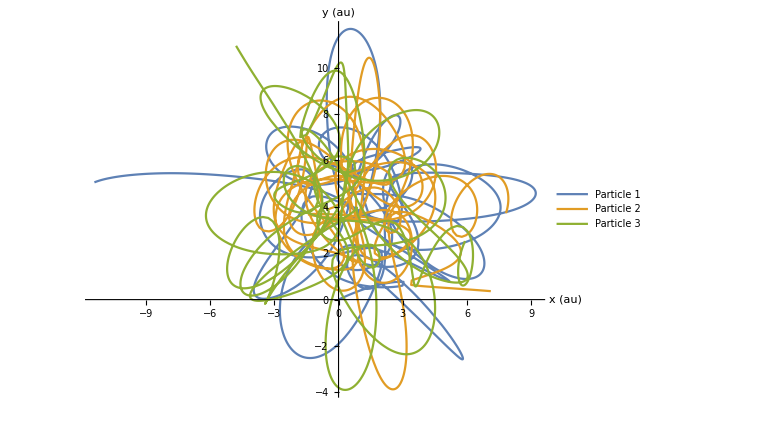

```mathematica
(*Define gravitational constant G in astronomical units (au),solar masses,and years*)
G=4 π^2; 
(*G=4π.b2 when using au,solar masses,and years*)

(*Define initial conditions*)
(*Particle 1*)
pos1={0,0}; (*au*)
vel1={0,10}*(1/(1.496*^8*365.25*24*3600)); (*Convert km/s to au/year*)

SeedRandom[12];
(*Particle 2-sample within ranges*)
q2x=RandomReal[{5,20}]; (*au*)
q2y=RandomReal[{0,10}]; (*au*)
pos2={q2x,q2y}; (*au*)
vel2={-10,0}*(1/(1.496*^8*365.25*24*3600)); (*Convert km/s to au/year*)

(*Particle 3-sample within ranges*)
q3x=RandomReal[{-10,0}]; (*au*)
q3y=RandomReal[{5,20}]; (*au*)
pos3={q3x,q3y}; (*au*)
vel3={0,0}*(1/(1.496*^8*365.25*24*3600)); (*Convert km/s to au/year*)

(*Define masses (assume equal masses for simplicity)*)
m1=1; (*mass of Particle 1*)
m2=1; (*mass of Particle 2*)
m3=1; (*mass of Particle 3*)

(*Define the system of differential equations*)
eq={
x1''[t]==G m2 (x2[t]-x1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (x3[t]-x1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,y1''[t]==G m2 (y2[t]-y1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (y3[t]-y1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,x2''[t]==G m1 (x1[t]-x2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (x3[t]-x2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,y2''[t]==G m1 (y1[t]-y2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (y3[t]-y2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,x3''[t]==G m1 (x1[t]-x3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (x2[t]-x3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3,y3''[t]==G m1 (y1[t]-y3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (y2[t]-y3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3};

(*Define initial conditions for the solver*)
init={
x1[0]==pos1[[1]],y1[0]==pos1[[2]],
x2[0]==pos2[[1]],y2[0]==pos2[[2]],
x3[0]==pos3[[1]],y3[0]==pos3[[2]],
x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],
x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],
x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};

(*Solve the system of differential equations*)
sol=NDSolve[{eq,init},{x1,y1,x2,y2,x3,y3},{t,0,100}];

(*Extract the trajectories*)
traj1={x1[t],y1[t]}/. sol;
traj2={x2[t],y2[t]}/. sol;
traj3={x3[t],y3[t]}/. sol;

(*Generate key from trajectories*)
(*Sample positions at discrete time steps*)
timeSteps=Range[0,100,0.01]; (*Sample every 0.1 years*)
positions=Flatten[Table[{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]}/. sol,{t,timeSteps}],1];



(*Flatten positions into a single list*)keyData=Flatten[positions];
Print["Key data length: ",Length[keyData]];
Print["First 100 numbers of the key data: ",Take[keyData,100]];

(*Convert key data to binary form*)
binaryKeyData=IntegerDigits[Round[Abs[keyData]*10^6],2,24];


(*Flatten the binary digits*)
flattenedBinaryKey=Flatten[binaryKeyData];

(*Generate a pseudo-random sequence*)
randomSequence=RandomInteger[{0,1},Length[flattenedBinaryKey]];

(*Apply XOR operation*)
key=BitXor[flattenedBinaryKey,randomSequence];


Print["Key length: ",Length[key]];
Print["Counts:",Counts[key]];


(*Plot the trajectories*)
ParametricPlot[{traj1,traj2,traj3},{t,0,100},PlotLegends->{"Particle 1","Particle 2","Particle 3"},AxesLabel->{"x (au)","y (au)"},PlotRange->All,ImageSize->Large]
```

```mathematica
(*SerialRandomnessTest*)
serialResult=N@ResourceFunction["SerialRandomnessTest"][key,"TestStatistic"];
serialPValue=N@ResourceFunction["SerialRandomnessTest"][key,"PValue"];
Print["Serial Randomness Test:"];
Print["  Test Statistic: ",serialResult];
Print["  P-Value: ",serialPValue];
If[serialPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ChiSquareRandomnessTest*)
chiSquareResult=N@ResourceFunction["ChiSquareRandomnessTest"][key,"TestStatistic"];
chiSquarePValue=N@ResourceFunction["ChiSquareRandomnessTest"][key,"PValue"];
Print["\nChi-Square Randomness Test:"];
Print["  Test Statistic: ",chiSquareResult];
Print["  P-Value: ",chiSquarePValue];
If[chiSquarePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*BinaryRunRandomnessTest*)
binaryRunResult=N@ResourceFunction["BinaryRunRandomnessTest"][key,"TestStatistic"];
binaryRunPValue=N@ResourceFunction["BinaryRunRandomnessTest"][key,"PValue"];
Print["\nBinary Run Randomness Test:"];
Print["  Test Statistic: ",binaryRunResult];
Print["  P-Value: ",binaryRunPValue];
If[binaryRunPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ArcsineLawRandomnessTest*)
arcsineResult=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"TestStatistic"];
arcsinePValue=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"PValue"]; (*Force numeric evaluation*)
Print["\nArcsine Law Randomness Test:"];
Print["  Test Statistic: ",arcsineResult];
Print["  P-Value: ",arcsinePValue];
If[arcsinePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];
```

Serial Randomness Test:

Test Statistic: 3.44671

P-Value: 0.135223

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 0.054439

P-Value: 0.815512

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 719548.

P-Value: 0.38253

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.265752

P-Value: 0.689592

Result: Good randomness (p-value > 0.05)